```mathematica
SetDirectory[ToFileName[("FileName"/.NotebookInformation[EvaluationNotebook[]])[[1]]]];
Clear[Header,FileData12,len,f];f=Import["test_stat1+2-3.csv"];
FileData12=Take[f,{2,50001}];Header=Take[f,1];Clear[f]; f=Import["test_stat1+2-2.csv"];FileData13=Take[f,{2,50001}];Clear[f];Header
```

{{N,H1,H0,T1,T2,T3,T4 (max run),T5,T6(0),T8,K[+],K[-],Kdiff,PValue,Evalue,Keys,LCC Volts,Error}}

```mathematica
len12 = Length[FileData12];len13 = Length[FileData13];{len12,len13}
```

{50000,50000}

```mathematica
{55000,50000}
```

{55000,50000}

```mathematica
Err1=Select[FileData12,#[[18]]≠0 &]; Pe12=N[Length[Err1]/(len12*20000)];Join[Header, Err1] // MatrixForm
```

(N | H1 | H0 | T1 | T2 | T3 | T4 (max run) | T5 | T6(0) | T8 | K[+] | K[-] | Kdiff | PValue | Evalue | Keys | LCC Volts | Error)

```mathematica
Err2=Select[FileData13,#[[17]]≠0 &]; Pe13=N[Length[Err2]/(len13*20000)];Join[Header, Err2] // MatrixForm
```

({N,H1,H0,T1,T2,T3,T4 (max run),T5,T6(0),T8,K[+],K[-],Kdiff,PValue,Evalue,Keys,LCC Volts,Error}
{1196,0.999002,1.05469,10372,39.5072,173,15,2495,0.0186,2.74448,4.5853,3.00416,1.58114,0.73273,34.088,12,21}
{40877,0.999086,1.0523,10356,49.3056,177,12,2494,0.0178,2.82296,4.26907,3.16228,1.1068,0.86377,30.4,12,21}
{49054,0.999106,1.0517,10352,39.392,146,14,2495,0.0176,2.82465,6.7989,1.89737,4.90153,0.62663,36.544,12,21})

```mathematica
{Pe12,Pe13}
```

{0.,3.×10^-9}

```mathematica
{{Min[FileData12[[All,10]]],Max[FileData12[[All,10]]]},{Min[FileData13[[All,10]]],Max[FileData13[[All,10]]]}}//MatrixForm
```

(2.64897 | 2.84244
2.63659 | 2.83862)

```mathematica
{{Min[FileData12[[All,5]]],Max[FileData12[[All,5]]]},{Min[FileData13[[All,5]]],Max[FileData13[[All,5]]]}}//MatrixForm
```

(1.344 | 49.7088
2.0608 | 55.6288)

```mathematica
{{Min[FileData12[[All,2]]],Min[FileData12[[All,3]]]},{Min[FileData13[[All,2]]],Min[FileData13[[All,3]]]}} // MatrixForm
```

(0.999275 | 0.958477
0.999002 | 0.969593)

```mathematica
{{Min[FileData12[[All,14]]],Max[FileData12[[All,14]]]},{Min[FileData13[[All,14]]],Max[FileData13[[All,14]]]}} // MatrixForm
```

(0.38641 | 1.
0.28036 | 1.)

```mathematica
Ent12=Select[FileData12,#[[2]]<0.99913 &];Ent13=Select[FileData13,#[[2]]<0.99913 &];{Length[Ent12],Length[Ent13]}
```

{0,3}

```mathematica
PVal12=Select[FileData12,#[[14]]<0.8&];PVal13=Select[FileData13,#[[14]]<0.8&];{Length[PVal12],Length[PVal13]}
```

{349,475}

```mathematica
K012=Select[FileData12,#[[13]]==0 &];K013=Select[FileData13,#[[13]]==0 &];{Length[K012],Length[K013]}
```

{2703,2379}

```mathematica
{Min[FileData12[[All,14]]],Max[FileData13[[All,14]]]}
```

{0.38641,1.}

```mathematica
P1=Select[FileData12,#[[14]]==1&];Length[P1]
```

1093

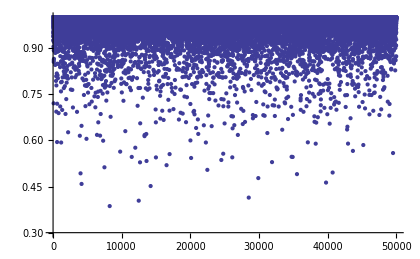
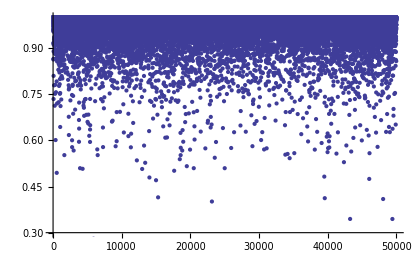
Chi Square Test (P-Value) QEKG I | Chi Square Test (P-Value) QEKG II
-Graphics- | -Graphics-

```mathematica
Grid[{{"Chi Square Test (P-Value) QEKG I","Chi Square Test (P-Value) QEKG II"},{ListPlot[FileData12[[All,14]],PlotRange->{0.3,1}, ImageSize->{420,300}],ListPlot[FileData13[[All,14]],PlotRange->{0.3,1},ImageSize->{420,300}]}} ,Frame->All]
```

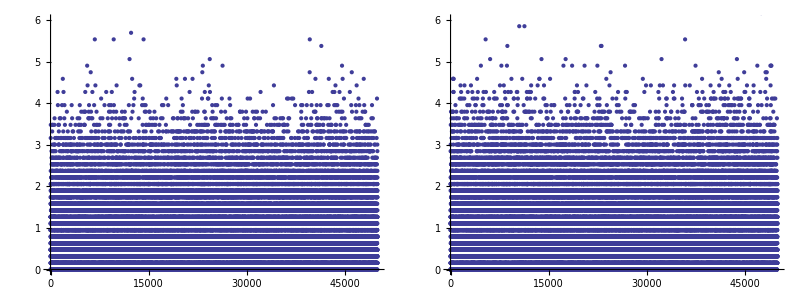

```mathematica
Grid[{{ListPlot[FileData12[[All,13]],PlotRange->{0,6}, ImageSize->{420,300}],ListPlot[FileData13[[All,13]],PlotRange->{0,6},ImageSize->{420,300}]}} ,Frame->All]
```

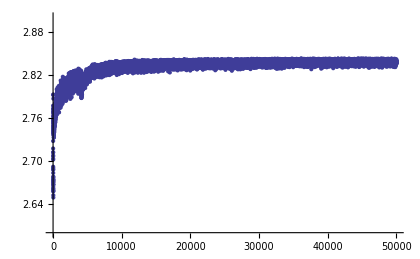
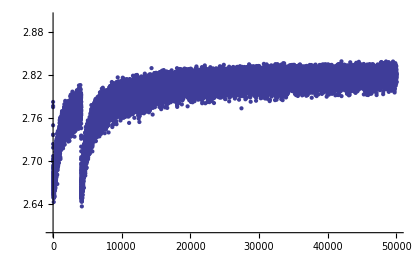
Test 8 ENT | Test 8 AMP
-Graphics- | -Graphics-

```mathematica
Grid[{{"Test 8 ENT","Test 8 AMP"},{ListPlot[FileData12[[All,10]],PlotRange->{2.6,2.9}, ImageSize->{420,300}],ListPlot[FileData13[[All,10]],PlotRange->{2.6,2.9},ImageSize->{420,300}]}} ,Frame->All]
```

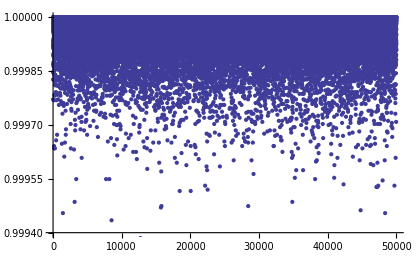
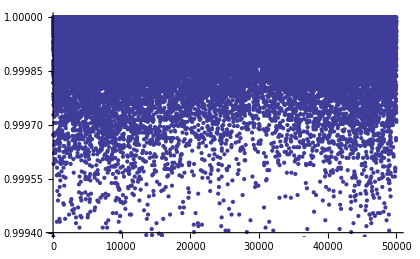
Entropy QEKG I | Entropy QEKG II
-Graphics- | -Graphics-

```mathematica
Grid[{{"Entropy QEKG I","Entropy QEKG II"},{ListPlot[FileData12[[All,2]],PlotRange->{0.9994,1}, ImageSize->{420,300}],ListPlot[FileData13[[All,2]],PlotRange->{0.9994,1},ImageSize->{420,300}]}} ,Frame->All]
```

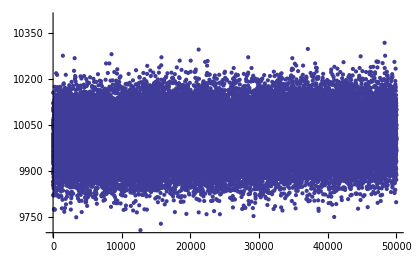
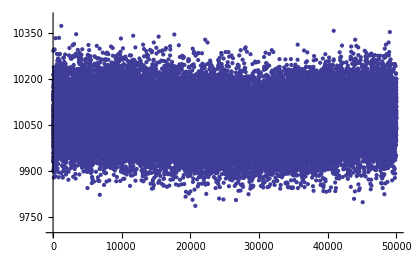
Monobit Test [FI140-1] (T1) QEKG I | Monobit Test [FI140-1] (T1) QEKG II
-Graphics- | -Graphics-

```mathematica
Grid[{{"Monobit Test [FI140-1] (T1) QEKG I", "Monobit Test [FI140-1] (T1) QEKG II"},{ListPlot[FileData12[[All,4]],PlotRange->{9700,10400}, ImageSize->{420,300}],ListPlot[FileData13[[All,4]],PlotRange->{9700,10400},ImageSize->{420,300}]}} ,Frame->All]
```

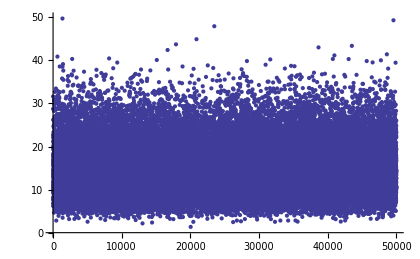
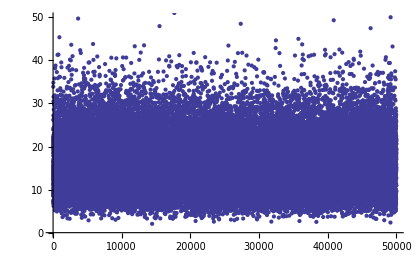
Block Test (T2) QEKG I | Block Test (T2) QEKG II
-Graphics- | -Graphics-

```mathematica
Grid[{{"Block Test (T2) QEKG I", "Block Test (T2) QEKG II"},{ListPlot[FileData12[[All,5]],PlotRange->{0,50}, ImageSize->{420,300}],ListPlot[FileData13[[All,5]],PlotRange->{0,50},ImageSize->{420,300}]}} ,Frame->All]
```

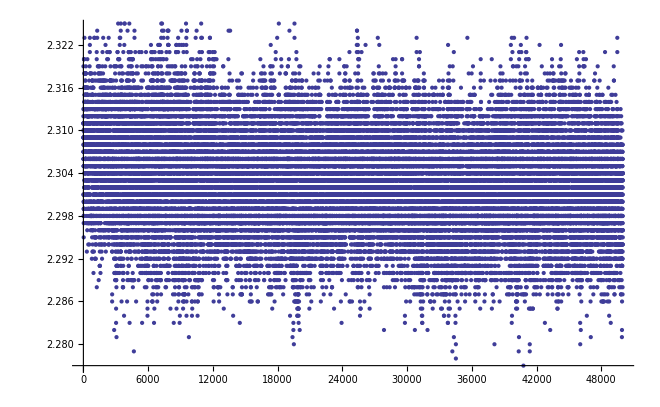

```mathematica
ListPlot[FileData12[[All,17]],PlotRange->{All}, ImageSize->{660,500}]
```